```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = RSS;
Hstar = HSS;
Fstar =FSS;

JacSpec = {
{D[dF,F],D[dF,H],D[dF,R]},
{D[dH,F],D[dH,H],D[dH,R]},
{D[dR,F],D[dR,H],D[dR,R]}
};
JacSpecSol = JacSpec/.{R->RSS,H->HSS,F->FSS};
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
(*Can't use analytic version because solution to Hopf must be numerically obtained*)
(*HopfAnalytic = Solve[Det[Sylv]==0,ρ];*)
```

```mathematica
Reps=100;
Opac=0.1;
SM=
Table[
MassValue=RandomReal[{1,9}]*10^0;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigvalues =N[ RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==10^-9},sig,{n,1,65}]];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>ConsumerGrowth&],
Joined->True,PlotRange->{{10^(-8),100},{10^(-8),100}},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->Directive[{Opacity[Opac],ColorData[97,1]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1]}],Line[{{Log@Growth/.M->MassValue,Log@(10^(-10))},{Log@Growth/.M->MassValue,Log@1000}}]}]
}],
{Reps}];
LM=
Table[
MassValue=RandomReal[{1,9}]*10^6;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigvalues =N[ RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==10^-9},sig,{n,1,65}]];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Re[HopfLine],
Joined->True,PlotRange->{{10^(-8),100},{10^(-8),100}},Frame->True,PlotStyle->Directive[{Opacity[Opac],ColorData[97,3]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3]}],Line[{{Log@Growth/.M->MassValue,Log@(10^(-10))},{Log@Growth/.M->MassValue,Log@1000}}]}]
}],
{Reps}];
```

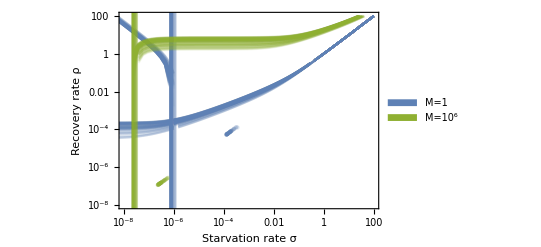

```mathematica
DataHopfPlot=Legended[Show[{
SM,
LM
}],Placed[SwatchLegend[{ColorData[97,1],ColorData[97,3]},{"M=1","M=10^6"},LegendMarkers->"Bubble"],{0.9,0.15}]]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf.pdf",DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_DataHopf_pre.pdf